```mathematica
$LoadFeynArts=True;
<<FeynCalc`
$FAVerbose=False;
```

FeynCalc 9.1.0. For help, use the documentation center, check out the wiki or write to the mailing list.

See also the supplied examples. If you use FeynCalc in your research, please cite

• V. Shtabovenko, R. Mertig and F. Orellana, Comput. Phys. Commun., 207C, 432-444, 2016, arXiv:1601.01167

• R. Mertig, M. Böhm, and A. Denner, Comput. Phys. Commun., 64, 345-359, 1991.

FeynArts 3.9 patched for use with FeynCalc, for documentation use the manual or visit www.feynarts.de.

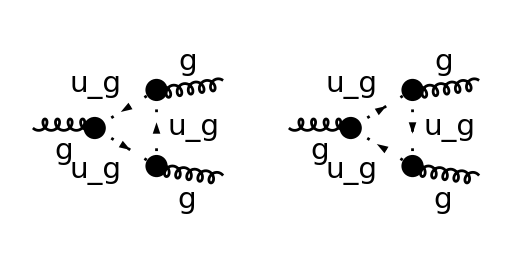

```mathematica
top=CreateTopologies[1,1->2,ExcludeTopologies->{WFCorrections,SelfEnergies,Tadpoles}];
diags=InsertFields[top,{V[5]}->{V[5],V[5]},Model->"SMQCD",InsertionLevel -> {Particles},ExcludeParticles->{F[__],S[_],V[_],U[1|2|3|4]}];
Paint[diags, ColumnsXRows -> {2, 1},SheetHeader -> False,SheetHeader->None,Numbering -> None,ImageSize->{512,256}];
```

```mathematica
amps=FCFAConvert[CreateFeynAmp[diags, Truncated -> True,GaugeRules->{},PreFactor->1],IncomingMomenta->{p1},
OutgoingMomenta->{p2,p3},LoopMomenta->{q},DropSumOver->True,UndoChiralSplittings->True,ChangeDimension->D,List->True,SMP->True,LorentzIndexNames->{λ,μ,ν},
SUNIndexNames->{a,b,c}]//Contract//SUNSimplify
```

{(ⅈ C_A g_s^3 q^μ (q-p2)^ν f^abc (-p2-p3+q)^λ)/(2 q^2.(q-p2)^2.(-p2-p3+q)^2),(ⅈ C_A g_s^3 q^λ (p2-q)^μ f^abc (p2+p3-q)^ν)/(2 q^2.(q-p2)^2.(-p2-p3+q)^2)}

```mathematica
amps2=amps[[2]]/.p3->-p2/.p2->p
```

-(ⅈ C_A g_s^3 q^λ q^ν (p-q)^μ f^abc)/(2 q^2.(q-p)^2.q^2)

```mathematica
amps1=amps[[1]]/.p3->-p2/.p2->p
```

(ⅈ C_A g_s^3 q^λ q^μ (q-p)^ν f^abc)/(2 q^2.(q-p)^2.q^2)

```mathematica
aaa=amps1+amps2;
fcaa=OneLoopSimplify[aaa,q];
AA=OneLoop[q,fcaa]
```

ⅈ π^2 (-1/(4 (1-D) (p̄)^2)C_A g_s^3 B_0((p̄)^2,0,0) (-D (p̄)^λ (p̄)^μ (p̄)^ν-(p̄)^2 (p̄)^ν (ḡ)^λμ+(p̄)^2 (p̄)^λ (ḡ)^μν-(p̄)^2 (p̄)^μ (ḡ)^λν+2 (p̄)^λ (p̄)^μ (p̄)^ν) (tr(T^a.T^b.T^c)-tr(T^b.T^a.T^c))-(C_A g_s^3 (p̄)^λ C_0(0,(p̄)^2,(p̄)^2,0,0,0) (-D (p̄)^μ (p̄)^ν-(p̄)^2 (ḡ)^μν+2 (p̄)^μ (p̄)^ν) (tr(T^a.T^b.T^c)-tr(T^b.T^a.T^c)))/(4 (1-D)))

```mathematica
Simplify[AA//.{FCI[C0[0,SP[p,p],SP[p,p],0,0,0]]->-(((-3+D) B0[FCI[SP[p,p]],0,0])/SP[p,p]),FCI[B0[FCI[SP[p,p]],0,0]]->1/(16*Epsilon*Pi^4)}];
Series[FCI[%]/.D->4-2 Epsilon,{Epsilon,0,0}]//Normal//Collect2[#,Epsilon]&
SelectNotFree[%,1/Epsilon]
```

(ⅈ C_A g_s^3 (2 (p̄)^λ (ḡ)^μν-(p̄)^μ (ḡ)^λν-(p̄)^ν (ḡ)^λμ) (tr(T^a.T^b.T^c)-tr(T^b.T^a.T^c)))/(192 π^2 ε)-(ⅈ C_A g_s^3 ((p̄)^2 (p̄)^ν (ḡ)^λμ+(p̄)^2 (p̄)^λ (ḡ)^μν+(p̄)^2 (p̄)^μ (ḡ)^λν+6 (p̄)^λ (p̄)^μ (p̄)^ν) (tr(T^a.T^b.T^c)-tr(T^b.T^a.T^c)))/(288 π^2 (p̄)^2)

(ⅈ C_A g_s^3 (2 (p̄)^λ (ḡ)^μν-(p̄)^μ (ḡ)^λν-(p̄)^ν (ḡ)^λμ) (tr(T^a.T^b.T^c)-tr(T^b.T^a.T^c)))/(192 π^2 ε)

```mathematica
ints=FCI[{FCI[B0[SP[p,p],0,0]]->1/(16*Epsilon*Pi^4),FCI[C0[0,SP[p,p],SP[p,p],0,0,0]]->-1/(16*Epsilon*Pi^4*SP[p,p])}]
Series[AA/.ints/.D->4-2 Epsilon,{Epsilon,0,0}]//Normal//Collect2[#,Epsilon]&
SelectNotFree[%,1/Epsilon]
```

{B_0((p̄)^2,0,0)→1/(16 π^4 ε),C_0(0,(p̄)^2,(p̄)^2,0,0,0)→-1/(16 π^4 ε (p̄)^2)}

(ⅈ C_A g_s^3 (2 (p̄)^λ (ḡ)^μν-(p̄)^μ (ḡ)^λν-(p̄)^ν (ḡ)^λμ) (tr(T^a.T^b.T^c)-tr(T^b.T^a.T^c)))/(192 π^2 ε)+(ⅈ C_A g_s^3 (2 (p̄)^λ (ḡ)^μν-(p̄)^μ (ḡ)^λν-(p̄)^ν (ḡ)^λμ) (tr(T^a.T^b.T^c)-tr(T^b.T^a.T^c)))/(288 π^2)

(ⅈ C_A g_s^3 (2 (p̄)^λ (ḡ)^μν-(p̄)^μ (ḡ)^λν-(p̄)^ν (ḡ)^λμ) (tr(T^a.T^b.T^c)-tr(T^b.T^a.T^c)))/(192 π^2 ε)